## Using the DFT: A Case Study

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Fortunately, Mathematica makes it easy to do spectral analysis with the DFT by providing a number of simple commands that carry out the required calculations and manipulations. It is not necessary to program the sum

X[n] =  ∑_(k=0)^(N-1) x[k] ⅇ^(-j (2π)/N k n), 0≤ n ≤ N-1

or the equivalent matrix multiplication

(X[0]
X[1]
⋮
X[N-1]) = (1 | 1 | 1 | … | 1
1 | ⅇ^(-j (2π)/N) | ⅇ^(-j (2π)/N 2) | ⋯ | ⅇ^(-j (2π)/N (N-1))
⋮ | ⋮ | ⋮ | ⋯ | ⋮
1 | ⅇ^(-j (2π)/N(N-1)) | ⅇ^(-j (2π)/N 2(N-1)) | ⋯ | ⅇ^(-j (2π)/N(N-1)(N-1))) .(x[0]
x[1]
⋮
x[N-1])

The single line commands Fourier[] and InverseFourier[] invoke efficient FFT (and IFFT) routines when possible, and relatively inefficient DFT (and IDFT) calculations otherwise. The numerical idiosyncrasies are mostly transparent. While the Fourier[ ] and InverseFourier[ ] commands are easy to invoke, their meaning is not always instantly transparent. This notebook provides some examples that show how to interpret (and how not to interpret) the output of the frequency analysis commands. 

To begin, consider a simple sine wave of frequency f=10 Hz. This plot shows the wave for 2.0 seconds.

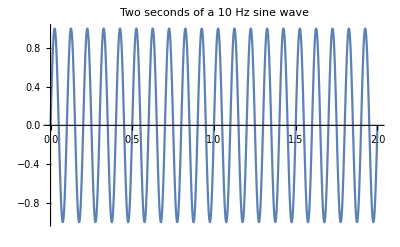

```mathematica
Plot[Sin[2 Pi 10 t],{t,0,2},PlotLabel->"Two seconds of a 10 Hz sine wave"]
```

The Fourier Transform of this is

```mathematica
FourierTransform[Sin[2 Pi 10 t],t,f, FourierParameters->{0,2 Pi}]
```

1/2 ⅈ DiracDelta[-10+f]-1/2 ⅈ DiracDelta[10+f]

which can't really be plotted properly since the answer is zero everywhere, except it is "infinity" at f0=10 and -f0=-10. Nonetheless, the Fourier Transform of a sinusoid is often drawn like this:

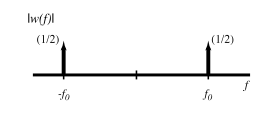

-Graphics-

A similar function that we can draw nice pictures for is a damped sinusoid like this:

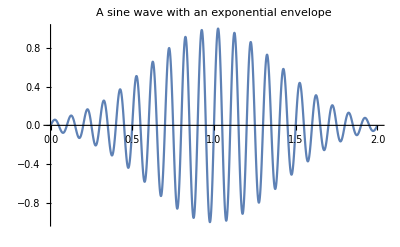

```mathematica
Plot[Exp[-3 (t-1)^2] Sin[2 Pi 10 t],{t,0,2},PlotLabel->"A sine wave with an exponential envelope"]
```

```mathematica
fftBurst[w_]:=FourierTransform[Exp[-3 (t-1)^2] Sin[2 Pi 10 t],t,w,FourierParameters->{0,2 Pi}]
```

The answer to this integration problem is

```mathematica
fftBurst[w]
```

1/2 ⅈ √(π/3) Cosh[1/3 π (-10+w) (-6 ⅈ-10 π+π w)]-1/2 ⅈ √(π/3) Cosh[1/3 π (10+w) (-6 ⅈ+10 π+π w)]-1/2 ⅈ √(π/3) Sinh[1/3 π (-10+w) (-6 ⅈ-10 π+π w)]+1/2 ⅈ √(π/3) Sinh[1/3 π (10+w) (-6 ⅈ+10 π+π w)]

which can be simplified some by considering just the magnitude

```mathematica
ComplexExpand[Abs[fftBurst[w]]]//FullSimplify
```

√(π/3) √(ⅇ^(-2/3 π^2 (100+w^2)) Sinh[(20 π^2 w)/3]^2)

But it is still not easy to understand. Fortunately, it is easy to plot, and then the answer makes a lot of sense: the transform is approximately a pair of spikes at the frequencies f = +/-10 Hz.

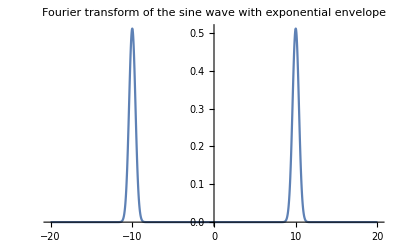

```mathematica
Plot[Abs[fftBurst[w]],{w,-20,20},PlotRange->All,PlotLabel->"Fourier transform of the sine wave with exponential envelope"]
```

The Fourier Transform and the FourierTransform[ ] command only apply to functions, that is, the signal that is to be transformed is required to be defined as a function. It is far more common (at least in signal processing applications) to have a bunch of data and to want to analyze that data, and this is the job of the DFT and Mathematica's Fourier[ ] command. The Fourier command can be applied to any set of data, real or complex valued. But first, to gain some intuition about its behavior, consider redoing the above two examples. 

First, it is necessary to sample the functions (in order to get the simulated data). The Nyquist theory tells us we must sample at least twice the rate of the highest frequency, but it's better to sample a bit faster than this, if possible. For this example, sample at every Ts=0.0026 seconds, which is about 380 times per second. This is well above the Nyquist rate for a 10 Hz sine wave!

```mathematica
Ts = 0.0026;
sinData = Table[Sin[2 Pi 10 t],{t,0,2,Ts}];
expData = Table[Exp[-3 (t-1)^2] Sin[2 Pi 10 t],{t,0,2,Ts}];
```

Here are ListPlots of the points

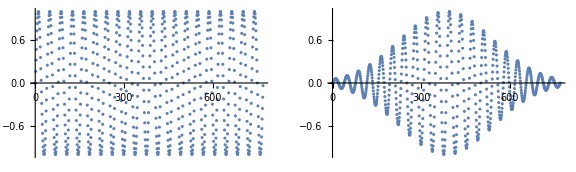
-Graphics-Sampled versions of the sine wave and the sine wave with exponential envelope

```mathematica
Labeled[GraphicsRow[{ListPlot[sinData],ListPlot[expData]},ImageSize->Large],"Sampled versions of the sine wave and the sine wave with exponential envelope",LabelStyle->captionStyle]
```

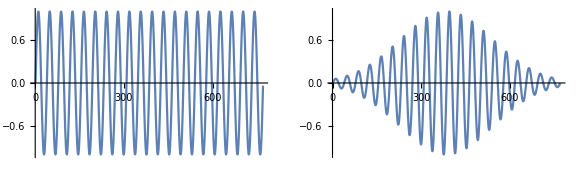
-Graphics-The points can be joined together to make the pictures look more like the underlying functions

```mathematica
Labeled[GraphicsRow[{ListPlot[sinData, Joined->True],ListPlot[expData, Joined->True, PlotRange->All]},ImageSize->Large],"The points can be joined together to make the pictures look more like the underlying functions",LabelStyle->captionStyle]
```

Let's just apply the Fourier[ ] command and hope for the best.

```mathematica
fftSinData = Fourier[sinData];
Length[fftSinData]
```

770

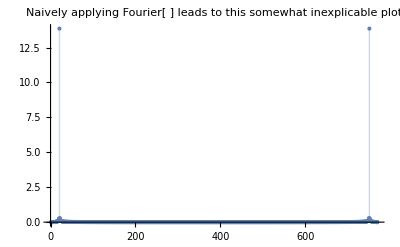

```mathematica
ListPlot[Abs[fftSinData], PlotRange->All,Filling->Axis,PlotLabel->"Naively applying Fourier[ ] leads to this somewhat inexplicable plot"]
```

Make sure to apply Abs[ ] (since the data is now complex-valued) or nothing appears in the plot. There are about 770 data points, and two of them are large. These occur at locations

```mathematica
maxPoints = Ordering[Abs[fftSinData],-2]
```

{21,751}

Zooming in on the first 50 or so, and looking at a log plot shows the values more clearly. But it doesn't show what they mean. Sure there is a big value at sample 21. What happened to the 10 Hz that we know constitutes this signal?

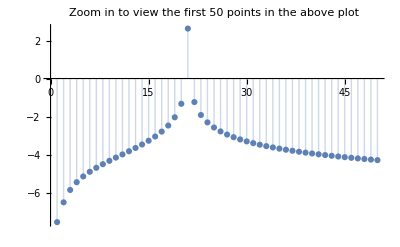

```mathematica
ListPlot[Log[Abs[fftSinData[[1;;50]]]], PlotRange->All,Filling->Axis,PlotLabel->"Zoom in to view the first 50 points in the above plot"]
```

There are several wrong with this:

(1) use the FourierParameters->{1,-1} option to use the right equation for the DFT
(2) the horizontal axis needs to be corrected
(3) the sampling rate needs to be taken into account
After these are corrected, the interpretation of the DFT will be analogous to the interpretation of the FT, that is, the output of Fourier[] will closely resemble the output of FourierTransform. The first two are easy:

```mathematica
fftSinData2 = Fourier[sinData,FourierParameters->{1,-1}];
numSam = Length[sinData];
fftSinData3 = RotateLeft[fftSinData,Round[numSam/2]];
```

Taking the sampling rate into account means that we have to know the meaning (in Hz) of one time sample. The rate chosen is Ts seconds per sample. There are numSam samples in the two seconds. So the meaning of each sample in frequency is

```mathematica
freqInd = 1/(Ts numSam)
```

0.4995

freqInd is in Hz. So the first element is the DC term, and each successive element is freqInd Hz higher than the last. The ssf vector will now give the correct frequency value to assign to every sample in the spectrum.

```mathematica
ssf = freqInd Range[-numSam/2,numSam/2-1];
```

Thus the meaning in frequency of the peaks can now be given in terms of the ssf vector.

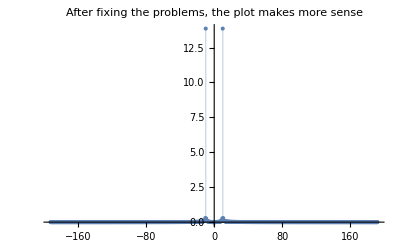

```mathematica
ListPlot[Transpose[{ssf,Abs[fftSinData3]}] ,PlotRange->All,Filling->Axis,PlotLabel->"After fixing the problems, the plot makes more sense"]
```

The peaks occur at indices 366 and 406

```mathematica
maxPoints = Ordering[Abs[fftSinData3],-2]
```

{366,406}

Which are the plus and minus components of the sinusoid at (approximately) 10 Hz!

```mathematica
{ssf[[366]], ssf[[406]]}
```

{-9.99001,9.99001}

Here is the plot one commonly draws with the frequency axis correct (meaning that it represents the frequency of the signal in Hz).

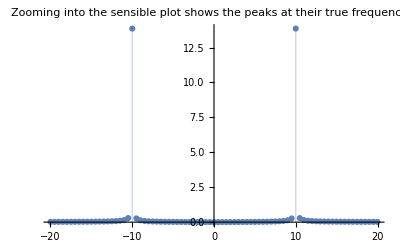

```mathematica
ListPlot[Transpose[{ssf[[346;;426]],Abs[fftSinData3][[346;;426]]}] ,PlotRange->All,Filling->Axis,PlotLabel->"Zooming into the sensible plot shows the peaks at their true frequencies"]
```

Finally, the meaning of the peaks is clear, and it is possible to see the two (expected) spikes at the correct frequency 9.99 Hz. While it took a fair bit of thought to get this right the first time, it is not hard to do, in general. For example, consider the expData function above. Given the sampling rate Ts and the data, here's everything:

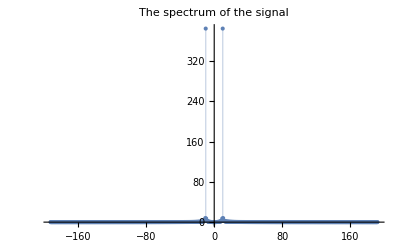

```mathematica
numSam = Length[expData]; 
freqInd = 1/(Ts numSam);
fftExpData = RotateLeft[Fourier[sinData,FourierParameters->{1,-1}],Round[numSam/2]];
ssf = freqInd Range[-numSam/2,numSam/2-1];
ListPlot[Transpose[{ssf,Abs[fftExpData]}] ,PlotRange->All,Filling->Axis,PlotLabel->"The spectrum of the signal"]
```

The maxima occur here:

```mathematica
maxPoints = Ordering[Abs[fftExpData],-2]
```

{366,406}

So the peaks are again at about +/- 10 Hz. Here is a zoomed version with a Log axis to see the variation better.

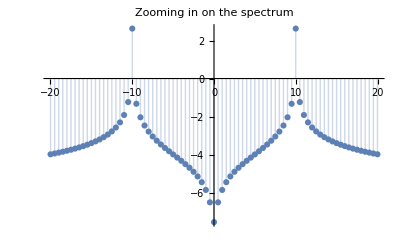

```mathematica
ListPlot[Transpose[{ssf[[346;;426]],Log[Abs[fftSinData3][[346;;426]]]}] ,PlotRange->All,Filling->Axis,PlotLabel->"Zooming in on the spectrum"]
```

Let's try the same kind of analysis on a real signal. Here's the sound of a gong. Press the little play button to hear it.

```mathematica
gong = -Graphics-;
```

Sounds are held in the same kind of "container" as images, so we need to extract the sound data and the sampling rate.

```mathematica
gongData = Flatten[gong[[1,1]]];
gongTs = 1./gong[[1,2]];
```

Plot the sound in time to see what it looks like:

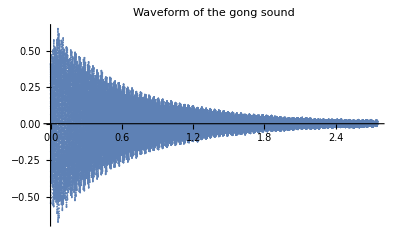

```mathematica
numSam = Length[gongData];
timeAxis=gongTs Range[1,numSam];
ListPlot[Transpose[{timeAxis,gongData}],PlotRange->All,PlotLabel->"Waveform of the gong sound"]
```

Here's the spectrum:

```mathematica
numSam = Length[gongData];
freqInd = 1/(gongTs numSam);
fftGongData = RotateLeft[Fourier[gongData,FourierParameters->{1,-1}],Round[numSam/2]];
ssf = freqInd Range[-numSam/2,numSam/2-1];
ListPlot[Transpose[{ssf,Abs[fftGongData]}] ,PlotRange->All,Filling->Axis,PlotLabel->"Spectrum of the gong sound"]
```

-Graphics-

It's all scrunched up around zero Hz so it's hard to see. Here's a zoomed in version:

```mathematica
mid = Ceiling[numSam/2]; z = 3000;
```

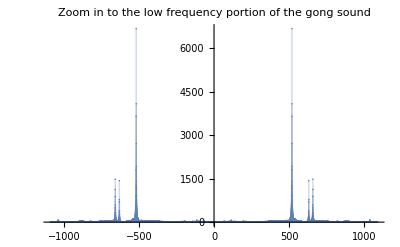

```mathematica
ListPlot[Transpose[{ssf[[mid-z;;mid+z]],Abs[fftGongData[[mid-z;;mid+z]]]}] ,PlotRange->All,Filling->Axis,PlotLabel->"Zoom in to the low frequency portion of the gong sound"]
```

This sound consists primarily of three major frequencies, at about 520, 630, and 660 Hz. Physically, these represent the three largest resonant modes of the vibrating plate.